```mathematica
This example has a single maximum at the origin of order 6.
```

19.0981 at example has maximum of order origin single the This

```mathematica
g[x_]:=1+(1/2)((10/16)*(Sin[x]^2)-2*Sin[x/2]^2-(1/32)*Sin[2*x]^2)
```

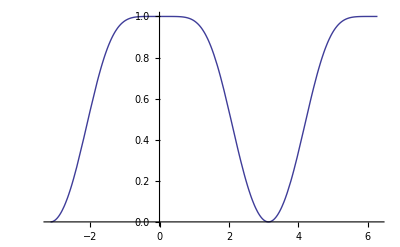

```mathematica
Plot[g[x],{x,-π,2*π}]
```

```mathematica
h[x_]=Log[g[x]]
```

Log[1+1/2 (-2 Sin[x/2]^2+(5 Sin[x]^2)/8-1/32 Sin[2 x]^2)]

```mathematica
Simplify[Series[h[x],{x,0,6}]]
```

-x^6/32+O[x]^7

```mathematica
This example has two maxima however they are of different orders so one of them will be scaled out
```

```mathematica
g[x_]:=1+((10/16)*(Sin[x]^2)-2*Sin[x/2]^2-(1/32)*Sin[2*x]^2)
```

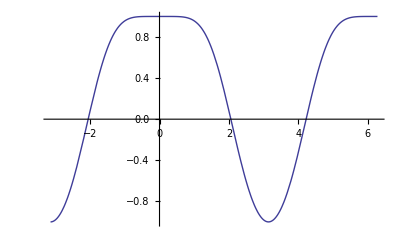

```mathematica
Plot[g[x],{x,-π,2*π}]
```

```mathematica
h[x_]=Log[g[x]]
```

Log[1-2 Sin[x/2]^2+(5 Sin[x]^2)/8-1/32 Sin[2 x]^2]

```mathematica
Simplify[Series[h[x],{x,0,6}]]
```

-x^6/16+O[x]^7

```mathematica
Simplify[Series[h[x],{x,π,6}]]
```

ⅈ π-(x-π)^2-5/12 (x-π)^4-137/720 (x-π)^6+O[x-π]^7

```mathematica
Here is a try at 4 in y and 6 in x
This next example can be simplified as 1+((5/16)*(Sin[x]^2)-Sin[x/2]^2-(1/64)*Sin[2*x]^2);
g[x_]=83/128+(1/4)ⅇ^(ⅈ*x)+(1/4)*ⅇ^(-ⅈ*x)-(5/64)ⅇ^(2ⅈ*x)-(5/64)*ⅇ^(-2ⅈ*x)+(1/256)ⅇ^(4ⅈ*x)+(1/256)*ⅇ^(-4ⅈ*x)
Plot[g[x],{x,-π,2*π}]
h[x_]=Log[g[x]]
Simplify[Series[h[x],{x,0,6}]]
```

24 (1/2+1/2 (1/2+(√3)/2)+1/4 √3 (-1+√3)+1/4 (5+√3)) and at Here in^2 is try x y

83/128+ⅇ^(-ⅈ x)/4+ⅇ^(ⅈ x)/4-5/64 ⅇ^(-2 ⅈ x)-5/64 ⅇ^(2 ⅈ x)+1/256 ⅇ^(-4 ⅈ x)+1/256 ⅇ^(4 ⅈ x)

-Graphics-

Log[83/128+ⅇ^(-ⅈ x)/4+ⅇ^(ⅈ x)/4-5/64 ⅇ^(-2 ⅈ x)-5/64 ⅇ^(2 ⅈ x)+1/256 ⅇ^(-4 ⅈ x)+1/256 ⅇ^(4 ⅈ x)]

-x^6/32+O[x]^7

```mathematica
g[x_,y_]=163/256+(1/8)ⅇ^(ⅈ*x)+(1/8)*ⅇ^(-ⅈ*x)-(5/128)ⅇ^(2ⅈ*x)-(5/128)*ⅇ^(-2ⅈ*x)+(1/512)ⅇ^(4ⅈ*x)+(1/512)*ⅇ^(-4ⅈ*x)+(1/8)ⅇ^(ⅈ*y)+(1/8)*ⅇ^(-ⅈ*y)-(1/32)ⅇ^(2ⅈ*y)-(1/32)*ⅇ^(-2ⅈ*y)
g[0,0]
Plot3D[Abs[g[x,y]],{x,-π,π},{y,-π,π}]
h[x_,y_]=Log[g[x,y]/g[0,0]];
Simplify[Series[h[x,y],{x,0,6},{y,0,4}]]
```

163/256+ⅇ^(-ⅈ x)/8+ⅇ^(ⅈ x)/8-5/128 ⅇ^(-2 ⅈ x)-5/128 ⅇ^(2 ⅈ x)+1/512 ⅇ^(-4 ⅈ x)+1/512 ⅇ^(4 ⅈ x)+ⅇ^(-ⅈ y)/8+ⅇ^(ⅈ y)/8-1/32 ⅇ^(-2 ⅈ y)-1/32 ⅇ^(2 ⅈ y)

1

-Graphics3D-

(-y^4/32+O[y]^5)+(-1/64-y^4/2048+O[y]^5) x^6+O[x]^7

```mathematica
The following is an example with a single attractor. Its polynomials expansion is not diagonal and it goes on the order of 4 in y and 6 in x.
```

```mathematica
g[x_,y_]=163/256+(1/8)ⅇ^(ⅈ*x)+(1/8)*ⅇ^(-ⅈ*x)-(5/128)ⅇ^(2ⅈ*x)-(5/128)*ⅇ^(-2ⅈ*x)+(1/512)ⅇ^(4ⅈ*x)+(1/512)*ⅇ^(-4ⅈ*x)+(1/8)ⅇ^(ⅈ*y)+(1/8)*ⅇ^(-ⅈ*y)-(1/32)ⅇ^(2ⅈ*y)-(1/32)*ⅇ^(-2ⅈ*y)+ⅈ*Sin[x]^3*Sin[y/2]^2/8
Plot3D[Abs[g[x,y]],{x,-π,π},{y,-π,π},AxesLabel->Automatic]
FourierSeries[g[x,y],{x,y},{4,4}]
FindMaximum[Abs[g[x,y]],{x},{y}]
g[0,0]
h[x_,y_]=Log[g[x,y]/g[0,0]];
Simplify[Series[h[x,y],{x,0,6},{y,0,4}]]
```

163/256+ⅇ^(-ⅈ x)/8+ⅇ^(ⅈ x)/8-5/128 ⅇ^(-2 ⅈ x)-5/128 ⅇ^(2 ⅈ x)+1/512 ⅇ^(-4 ⅈ x)+1/512 ⅇ^(4 ⅈ x)+ⅇ^(-ⅈ y)/8+ⅇ^(ⅈ y)/8-1/32 ⅇ^(-2 ⅈ y)-1/32 ⅇ^(2 ⅈ y)+1/8 ⅈ Sin[x]^3 Sin[y/2]^2

-Graphics3D-

163/256+(13 ⅇ^(-ⅈ x))/128+(19 ⅇ^(ⅈ x))/128-5/128 ⅇ^(-2 ⅈ x)-5/128 ⅇ^(2 ⅈ x)+1/128 ⅇ^(-3 ⅈ x)-1/128 ⅇ^(3 ⅈ x)+1/512 ⅇ^(-4 ⅈ x)+1/512 ⅇ^(4 ⅈ x)-1/256 ⅇ^(ⅈ (-3 x-y))+3/256 ⅇ^(ⅈ (-x-y))-3/256 ⅇ^(ⅈ (x-y))+1/256 ⅇ^(ⅈ (3 x-y))+ⅇ^(-ⅈ y)/8+ⅇ^(ⅈ y)/8-1/32 ⅇ^(-2 ⅈ y)-1/32 ⅇ^(2 ⅈ y)-1/256 ⅇ^(ⅈ (-3 x+y))+3/256 ⅇ^(ⅈ (-x+y))-3/256 ⅇ^(ⅈ (x+y))+1/256 ⅇ^(ⅈ (3 x+y))

{1.,{x→0.0165248,y→-0.00250174}}

1

(-y^4/32+O[y]^5)+((ⅈ y^2)/32-(ⅈ y^4)/384+O[y]^5) x^3+(-(ⅈ y^2)/64+(ⅈ y^4)/768+O[y]^5) x^5+(-1/64+O[y]^5) x^6+O[x]^7

```mathematica
g[x_,y_]=163/256+(13 ⅇ^(-ⅈ x))/128+(19 ⅇ^(ⅈ x))/128-5/128 ⅇ^(-2 ⅈ x)-5/128 ⅇ^(2 ⅈ x)+1/128 ⅇ^(-3 ⅈ x)-1/128 ⅇ^(3 ⅈ x)+1/512 ⅇ^(-4 ⅈ x)+1/512 ⅇ^(4 ⅈ x)-1/256 ⅇ^(ⅈ (-3 x-y))+3/256 ⅇ^(ⅈ (-x-y))-3/256 ⅇ^(ⅈ (x-y))+1/256 ⅇ^(ⅈ (3 x-y))+ⅇ^(-ⅈ y)/8+ⅇ^(ⅈ y)/8-1/32 ⅇ^(-2 ⅈ y)-1/32 ⅇ^(2 ⅈ y)-1/256 ⅇ^(ⅈ (-3 x+y))+3/256 ⅇ^(ⅈ (-x+y))-3/256 ⅇ^(ⅈ (x+y))+1/256 ⅇ^(ⅈ (3 x+y));
Plot3D[Abs[g[x,y]],{x,-π,π},{y,-π,π},AxesLabel->Automatic]
FourierSeries[g[x,y],{x,y},{4,4}]
FindMaximum[Abs[g[x,y]],{x},{y}]
g[0,0]
h[x_,y_]=Log[g[x,y]/g[0,0]];
Simplify[Series[h[x,y],{x,0,6},{y,0,4}]]
```

-Graphics3D-

163/256+(13 ⅇ^(-ⅈ x))/128+(19 ⅇ^(ⅈ x))/128-5/128 ⅇ^(-2 ⅈ x)-5/128 ⅇ^(2 ⅈ x)+1/128 ⅇ^(-3 ⅈ x)-1/128 ⅇ^(3 ⅈ x)+1/512 ⅇ^(-4 ⅈ x)+1/512 ⅇ^(4 ⅈ x)-1/256 ⅇ^(ⅈ (-3 x-y))+3/256 ⅇ^(ⅈ (-x-y))-3/256 ⅇ^(ⅈ (x-y))+1/256 ⅇ^(ⅈ (3 x-y))+ⅇ^(-ⅈ y)/8+ⅇ^(ⅈ y)/8-1/32 ⅇ^(-2 ⅈ y)-1/32 ⅇ^(2 ⅈ y)-1/256 ⅇ^(ⅈ (-3 x+y))+3/256 ⅇ^(ⅈ (-x+y))-3/256 ⅇ^(ⅈ (x+y))+1/256 ⅇ^(ⅈ (3 x+y))

{1.,{x→0.0112173,y→0.00287925}}

1

(-y^4/32+O[y]^5)+((ⅈ y^2)/32-(ⅈ y^4)/384+O[y]^5) x^3+(-(ⅈ y^2)/64+(ⅈ y^4)/768+O[y]^5) x^5+(-1/64+O[y]^5) x^6+O[x]^7

```mathematica
p[x_,y_]=y^4/32-ⅈ*y^2*x^3/32+x^6/64
Ft[x_,y_]=Exp[-p[x,y]]
Plot3D[Re[Ft[x,y]],{x,-π,π},{y,-π,π},AxesLabel->Automatic]
FourierTransform[Ft[x,y],{x,y},{0,1}]
```

x^6/64-1/32 ⅈ x^3 y^2+y^4/32

ⅇ^(-x^6/64+1/32 ⅈ x^3 y^2-y^4/32)

-Graphics3D-